```mathematica
α=-2;
β=-2;
h0=0;
h1=2;
```

```mathematica
(*Caso discontinuidad en x=Subscript[h, 0]*)A0={{Exp[k h0], Exp[-k h0]},{k Exp[k h0], -k Exp[-k h0]}};(*matriz Subscript[A, 0]*)
CA0={{1,0},{α,1}};(*matriz de condiciones de frontera*)
CD00={{c0},{0}};(*Matriz semilla*)
A00=Inverse[A0] . CA0 . A0;(*Matriz Subscript[M, 0]*)
A00[[1,1]]//Simplify
A00[[2,1]]//Simplify
```

(-1+k)/k

1/k

```mathematica
(*Caso discontinuidad en x=Subscript[h, 1]*)A1={{Exp[k h1], Exp[-k h1]},{k Exp[k h1], -k Exp[-k h1]}};(*matriz Subscript[A, 0]*)
CA1={{1,0},{β,1}};(*matriz de condiciones de frontera*)
A11=Inverse[A1] . CA1 . A1 . A00 . CD00;(*Matriz Subscript[M, 0]*)
```

```mathematica
A11[[1,1]]//Simplify(*Elemento correspondiente al término para la ecuación de dispersión*)
A11[[2,1]]//Simplify
```

(c0 (-ⅇ^(-4 k)+(-1+k)^2))/k^2

(c0 (1+ⅇ^(4 k) (-1+k)+k))/k^2

```mathematica
κ[k_]:=(-ⅇ^(-4 k)+(-1+k)^2)/k^2;(*Define la ecuación de dispersión*)
NSolve[κ[k]==0,k,Reals](*Obtiene eigen-valores*)
```

{{k→0.796812},{k→1.10886}}

```mathematica
NSolve[(-ⅇ^(-4 k)+(-1+k)^2)==0,k,Reals]
```

{{k→0.},{k→0.796812},{k→1.10886}}

```mathematica
kj={1.1088575528785451,0.79681213002002};(*Arreglo de k permitidos*)
ϕj[x_,n_]:=Piecewise[{{Exp[kj[[n]]x] ,x<0},{(-1+kj[[n]])/kj[[n]] Exp[kj[[n]]x]+1/kj[[n]] Exp[-kj[[n]]x] ,0<x<h1},{(1/(kj[[n]])^2(1+Exp[4kj[[n]]] (-1+kj[[n]])+kj[[n]])) Exp[-kj[[n]]x] ,x>h1}}];
(*Definición de la eigen-función*)
```

```mathematica
Mj[n_]:=√(∫_(-∞)^0 (Abs[ϕj[x,n]])^2 ⅆx+∫_0^2 (Abs[ϕj[x,n]])^2 ⅆx+∫_2^∞ (Abs[ϕj[x,n]])^2 ⅆx);(*Define las constantes de normalización*)
Mj[1]
Mj[2]
(*Obtenemos el elemento correspondiente para generar el arreglo de constantes de normalización*)
```

1.40738

1.36746

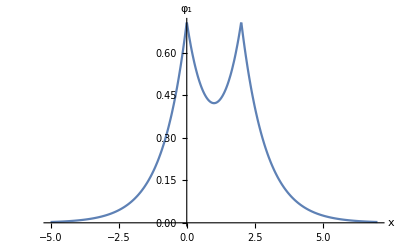

```mathematica
M={1.4073823025817092,1.367460787585445};(*Constantes de normalización de cada eigen-función*)
Plot[1/M[[1]] ϕj[x,1],{x,-5,7},PlotRange->All, AxesLabel->{Style[x,Medium],Style[Subscript[φ, 1],Medium]}](*Gráfica de la primer eigen-función*)
```

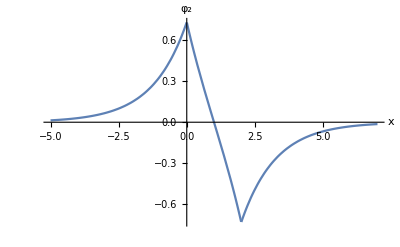

```mathematica
Plot[1/M[[2]] ϕj[x,2],{x,-5,7},PlotRange->All,AxesLabel->{Style[x,Medium],Style[Subscript[φ, 2],Medium]}](*Gráfica de la segunda eigen-función*)
```

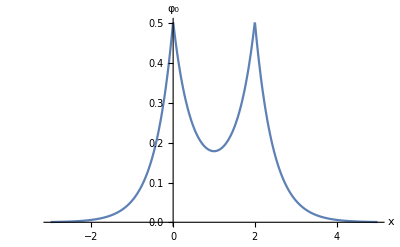

```mathematica
Plot[(Abs[1/M[[1]] ϕj[x,1]])^2,{x,-3,5},PlotRange->All,AxesLabel->{Style[x,Medium],Style[Subscript[φ, 0],Medium]}]
```

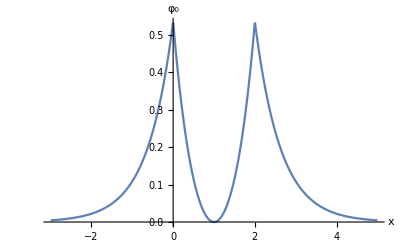

```mathematica
Plot[(Abs[1/M[[2]] ϕj[x,2]])^2,{x,-3,5},PlotRange->All,AxesLabel->{Style[x,Medium],Style[Subscript[φ, 0],Medium]}]
```